```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\4 Oscillators with NO Entanglement Present"];
```

```mathematica
LN125=ReadList["LNData_NM_beta_0.3_Oomega_1.25_Generating_Entanglement.txt"];
LN150=ReadList["LNData_NM_beta_0.3_Oomega_1.5_Generating_Entanglement.txt"];
LN175=ReadList["LNData_NM_beta_0.3_Oomega_1.75_Generating_Entanglement.txt"];
LN200=ReadList["LNData_NM_beta_0.3_Oomega_2_Generating_Entanglement.txt"];

ifunc125=Interpolation[LN125[[1]]];
ifunc150=Interpolation[LN150[[1]]];
ifunc175=Interpolation[LN175[[1]]];
ifunc200=Interpolation[LN200[[1]]];
```

```mathematica
plotwindowlength=50;
n=0;
Column[{
Dynamic[Show[{Plot[ifunc150[x], {x, n, n+plotwindowlength}, ImageSize->Medium, PlotRange->All], ListPlot[LN150[[1]][[2*n+1;;2*(n+plotwindowlength)+1]], ImageSize->Medium, PlotStyle->Red, PlotRange->All]}]], Row[{Dynamic[n], Slider[Dynamic[n],{0,0.5*(Length[LN175[[1]]]-1)-plotwindowlength,1}], Dynamic[n+plotwindowlength]}]
}]
```

```mathematica
LN100=ReadList["LNData_NM_beta_0.3_Oomega_1._Generating_Entanglement.txt"];
LN105=ReadList["LNData_NM_beta_0.3_Oomega_1.05_Generating_Entanglement.txt"];
LN110=ReadList["LNData_NM_beta_0.3_Oomega_1.1_Generating_Entanglement.txt"];
LN115=ReadList["LNData_NM_beta_0.3_Oomega_1.15_Generating_Entanglement.txt"];
LN120=ReadList["LNData_NM_beta_0.3_Oomega_1.2_Generating_Entanglement.txt"];
LN125=ReadList["LNData_NM_beta_0.3_Oomega_1.25_Generating_Entanglement.txt"];
LN130=ReadList["LNData_NM_beta_0.3_Oomega_1.3_Generating_Entanglement.txt"];
LN135=ReadList["LNData_NM_beta_0.3_Oomega_1.35_Generating_Entanglement.txt"];
LN140=ReadList["LNData_NM_beta_0.3_Oomega_1.4_Generating_Entanglement.txt"];
LN145=ReadList["LNData_NM_beta_0.3_Oomega_1.45_Generating_Entanglement.txt"];
LN150=ReadList["LNData_NM_beta_0.3_Oomega_1.5_Generating_Entanglement.txt"];
LN155=ReadList["LNData_NM_beta_0.3_Oomega_1.55_Generating_Entanglement.txt"];
LN160=ReadList["LNData_NM_beta_0.3_Oomega_1.6_Generating_Entanglement.txt"];
LN165=ReadList["LNData_NM_beta_0.3_Oomega_1.65_Generating_Entanglement.txt"];
LN170=ReadList["LNData_NM_beta_0.3_Oomega_1.7_Generating_Entanglement.txt"];
LN175=ReadList["LNData_NM_beta_0.3_Oomega_1.75_Generating_Entanglement.txt"];
LN180=ReadList["LNData_NM_beta_0.3_Oomega_1.8_Generating_Entanglement.txt"];
LN185=ReadList["LNData_NM_beta_0.3_Oomega_1.85_Generating_Entanglement.txt"];
LN190=ReadList["LNData_NM_beta_0.3_Oomega_1.9_Generating_Entanglement.txt"];
LN195=ReadList["LNData_NM_beta_0.3_Oomega_1.95_Generating_Entanglement.txt"];
LN200=ReadList["LNData_NM_beta_0.3_Oomega_2_Generating_Entanglement.txt"];
```

```mathematica
MeanData={
{1.00, Mean[Table[LN100[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.05, Mean[Table[LN105[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.10, Mean[Table[LN110[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.15, Mean[Table[LN115[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.20, Mean[Table[LN120[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.25, Mean[Table[LN125[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.30, Mean[Table[LN130[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.35, Mean[Table[LN135[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.40, Mean[Table[LN140[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.45, Mean[Table[LN145[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.50, Mean[Table[LN150[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.55, Mean[Table[LN155[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.60, Mean[Table[LN160[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.65, Mean[Table[LN165[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.70, Mean[Table[LN170[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.75, Mean[Table[LN175[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.80, Mean[Table[LN180[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.85, Mean[Table[LN185[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.90, Mean[Table[LN190[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{1.95, Mean[Table[LN195[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]},
{2.00, Mean[Table[LN200[[1]][[pt]][[2]], {pt, 2*50+1, 2*200+1}]]}
};
```

```mathematica
MeanData//MatrixForm
```

(1. | 0
1.05 | 0
1.1 | 0.00358342
1.15 | 0.0182832
1.2 | 0.0352982
1.25 | 0.0511245
1.3 | 0.0658623
1.35 | 0.0796022
1.4 | 0.0924385
1.45 | 0.104466
1.5 | 0.115769
1.55 | 0.12641
1.6 | 0.136437
1.65 | 0.145899
1.7 | 0.154854
1.75 | 0.16335
1.8 | 0.171418
1.85 | 0.179082
1.9 | 0.186369
1.95 | 0.193314
2. | 0.199946)

```mathematica
MeanDatafunc=NonlinearModelFit[MeanData, a*x^2+b*x+c, {a, b, c}, x]
```

FittedModel[…]

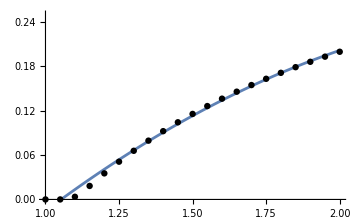
{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.0808948 | 0.0140528 | -5.7565 | 0.0000186271
b | 0.460082 | 0.0423286 | 10.8693 | 2.43976×10^-9
c | -0.394813 | 0.0308808 | -12.7851 | 1.80748×10^-10}
-Graphics-

```mathematica
Column[{MeanDatafunc[{"ParameterTable"}], 
Show[{Plot[MeanDatafunc[x], {x, 1, 2}, PlotRange->{0, 0.25}, ImageSize->Medium], ListPlot[MeanData, PlotStyle->Black]}]}]
```

```mathematica
MeanDataColorValues=Rescale[Table[MeanData[[pt]][[2]], {pt, 1, 21}]];
MeanDataColors=Table[ColorData["Pastel"][MeanDataColorValues[[value]]], {value, 1, 21}]
```

{RGBColor[0.761959, 0.470832, 0.940597],RGBColor[0.761959, 0.470832, 0.940597],RGBColor[0.7713697536810556, 0.49346110114030606, 0.943095178956057],RGBColor[0.8100274391135566, 0.5859809922216892, 0.9522072239093691],RGBColor[0.8632142715075793, 0.6440560070680887, 0.7823339909789602],RGBColor[0.9013815131507069, 0.6896904918012297, 0.6707630733190223],RGBColor[0.926652460520357, 0.7399689354989978, 0.6172357937829839],RGBColor[0.9437341684729796, 0.793980243967598, 0.5945120601800103],RGBColor[0.9552989000982064, 0.8483381905077755, 0.5877996098208152],RGBColor[0.9602898782687159, 0.8955020409643472, 0.5923704274267917],RGBColor[0.9570240603542814, 0.9282018195469008, 0.6088671477085902],RGBColor[0.9488174212437607, 0.9514875286795133, 0.6322676022589271],RGBColor[0.9193084917302616, 0.9488068175332515, 0.6807364582798027],RGBColor[0.8879379448413769, 0.9429061323291662, 0.7297290311865219],RGBColor[0.8288835279140553, 0.9148443349655423, 0.793762742108825],RGBColor[0.7728553409978696, 0.8882205579527538, 0.8545150602446079],RGBColor[0.6951605403847466, 0.8503946621889592, 0.898980368049613],RGBColor[0.6206453261750782, 0.8140985185989751, 0.9408256380515493],RGBColor[0.5532130301842778, 0.7781920425855868, 0.9483067869862611],RGBColor[0.49085076157806207, 0.7431947439714945, 0.9374474535814954],RGBColor[0.431296, 0.709773, 0.927077]}

```mathematica
height=400;
width=600;
PlotFormat1={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black, 20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20], PlotRange->All};

GenerateEntanglement=Plot[{ifunc125[x], ifunc150[x], ifunc175[x], ifunc200[x]}, {x, 0, 200}, PlotStyle->Table[Directive[MeanDataColors[[color]]], {color, 6, 21, 5}], PlotRange->{{0, 200}, {0, 0.21}}, Evaluate[PlotFormat1], Ticks->{Automatic, {0, 0.05, 0.10, 0.15, 0.20}}];
```

```mathematica
height=400;
width=600;
PlotFormat2={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"Ω=ω", "𝒩"}, AxesStyle->Directive[Black, 20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20]};
PlotFormat3={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width, FrameStyle->Directive[Black, 20], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 20]};

MeanValuePlotVersion1=Show[{Plot[MeanDatafunc[x], {x, 1, 2},  PlotStyle->Directive[Black, Dashed], PlotRange->{{0.9, 2.1}, {0, 0.21}}, Evaluate[PlotFormat2], Ticks->{Automatic, {0, 0.05, 0.10, 0.15, 0.20}}], ListPlot[Table[{MeanData[[value]]}, {value, 1, 20}], PlotStyle->Table[Directive[MeanDataColors[[color]], PointSize->0.02], {color, 1, 20}], Frame->True, FrameLabel->{None, None}]}];
```

```mathematica
SecondAxis=ListPlot[{None}, Frame->{{True, True}, {True, True}}, FrameLabel->{{"𝒩", ""}, {"τ", "Ω=ω"}}, FrameTicks->{{{0, 0.05, 0.1, 0.15, 0.2}, None}, {{0}, {0, 0.5, 1, 1.5, 2}}}, PlotRange->{{0, 2.1}, {0, 0.21}}, Evaluate[PlotFormat3]];
MeanValuePlotVersion2=Show[{SecondAxis, Plot[MeanDatafunc[x], {x, 1, 2},  PlotStyle->Directive[Black, Dashed], PlotRange->{{0.9, 2.1}, {0, 0.21}}, Frame->{{False, False}, {False, True}}, FrameLabel->{{"", ""}, {"", "Ω=ω"}}, Evaluate[PlotFormat3]], ListPlot[Table[{MeanData[[value]]}, {value, 1, 21}], PlotStyle->Directive[Black, PointSize->0.025]],
ListPlot[Table[{MeanData[[value]]}, {value, 1, 21}], PlotStyle->Table[Directive[MeanDataColors[[color]], PointSize->0.02], {color, 1, 21}]]}];
```

```mathematica
FirstAxis=ListPlot[{None}, Frame->{{True, True}, {True, True}}, FrameLabel->{{"𝒩", ""}, {"τ", "Ω=ω"}}, FrameTicks->{{{0, 0.05, 0.1, 0.15, 0.2}, None}, {{0, 50, 100, 150, 200}, {0}}}, PlotRange->{{0, 210}, {0, 0.21}}, Evaluate[PlotFormat3]];

GenerateEntanglementPlot=Show[{FirstAxis, GenerateEntanglement}];
```

```mathematica
FinalOutput=Rasterize[Overlay[{GenerateEntanglementPlot, MeanValuePlotVersion2}]]
```

-Graphics-

```mathematica
Export["Entanglement Generation from Vacuum States.png", FinalOutput]
```

Entanglement Generation from Vacuum States.png

```mathematica
LNTwoModeSqueezed150=ReadList["LNData_NM_beta_0.3_Oomega_1.5_Preserving_Entanglement.txt"];
LNTwoModeSqueezed100=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Oomega Resonance with eta_0 no Betamax\\Non-Markovian Entanglement Omega_1.00.txt"];
```

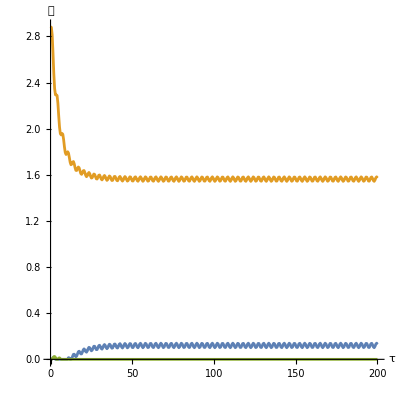
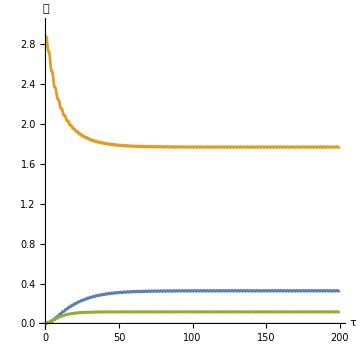

```mathematica
Row[{ListLinePlot[{LNTwoModeSqueezed100[[1]][[1;;401]], LNTwoModeSqueezed100[[2]][[1;;401]], LN100[[1]]}, Evaluate[PlotFormat1]], ListLinePlot[{LNTwoModeSqueezed150[[1]][[1;;401]], LNTwoModeSqueezed150[[6]][[1;;401]], LN150[[1]][[1;;401]]}, PlotRange->{0, 3},ImageSize->Medium, Evaluate[PlotFormat1]]}]
```

```mathematica
JustLN12=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\LN12_Vacuum_States_beta_0.3_Oomega_1.5.txt"];
JustLN34=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\LN34_Two-Mode_Squeezed_State_beta_0.3_Oomega_1.5.txt"];
```

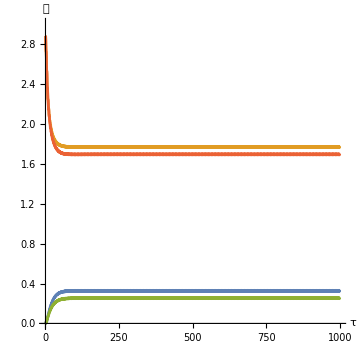

```mathematica
ListLinePlot[{LNTwoModeSqueezed150[[1]], LNTwoModeSqueezed150[[6]], JustLN12, JustLN34}, PlotRange->{0, 3},ImageSize->Medium, Evaluate[PlotFormat1]]
```

```mathematica
diff12=Table[{JustLN12[[pt]][[1]], Chop[LNTwoModeSqueezed150[[1]][[pt]][[2]]-JustLN12[[pt]][[2]]]}, {pt, 1, Length[JustLN12]}];
diff34=Table[{JustLN34[[pt]][[1]], Chop[LNTwoModeSqueezed150[[6]][[pt]][[2]]-JustLN34[[pt]][[2]]]}, {pt, 1, Length[JustLN34]}];
```

```mathematica
plotwindowlength=500;
n=0;
Column[{
Dynamic[ListLinePlot[{diff12[[2*n+1;;2*(n+plotwindowlength)+1]], diff34[[2*n+1;;2*(n+plotwindowlength)+1]]}, ImageSize->Medium, PlotStyle->{Directive[Blue], Directive[Dashed, Red]}, PlotRange->All]], Row[{Dynamic[n], Slider[Dynamic[n],{0,0.5*(Length[LN175[[1]]]-1)-plotwindowlength,1}], Dynamic[n+plotwindowlength]}]
}]
```